```mathematica
(*Simulations using linear programming and noisy data*)

(*The matrix defining hypergeometric sampling*)
mat[pop_,samp_]:=Table[Binomial[i,j]Binomial[pop-i,samp-j],{j,0,samp},{i,0,pop}]/Binomial[pop,samp]
```

```mathematica
(*Start with regular LP, but coarsen the last few bins (to see how much info  we loose) Here we are still assuming infinite data!*)

extrapolateCoarse[sampsize_,popsize_,max_,cut_]:=Module[{b,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]}; (*The model SFS*)
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;(*Normalize by # of SNPS--doesn't matter in this model*)
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
start=Apply[Plus, sub⟦1,2;;⟧];
exact=Apply[Plus, poploc⟦1,2;;⟧];
subcoarse=sub[[1]][[1;;cut+1]];
AppendTo[subcoarse,Apply[Plus,sub[[1]][[cut+2;;]]]];

bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"];

Return[{start, exact,c.sol,c.solmin}]



]
```

```mathematica
(*Explore convergence of linear programming converges as a function of number of bins used*)
nstart=50
nend=200
maxbins=20
output=ParallelTable[Timing[N[extrapolateCoarse[nstart,nend,nend,i]]],{i,1,maxbins}]
```

50

200

20

{{0.49223,{1410.56,1820.36,1501.52,2323.14}},{0.52117,{1410.56,1820.36,1629.59,2157.55}},{0.58966,{1410.56,1820.36,1664.84,1979.85}},{0.61596,{1410.56,1820.36,1715.57,1941.46}},{0.6892,{1410.56,1820.36,1732.16,1891.42}},{0.79685,{1410.56,1820.36,1751.91,1877.6}},{0.82048,{1410.56,1820.36,1758.2,1857.6}},{0.88742,{1410.56,1820.36,1782.46,1851.23}},{0.92337,{1410.56,1820.36,1789.8,1843.23}},{0.954189,{1410.56,1820.36,1800.71,1838.82}},{1.06491,{1410.56,1820.36,1803.98,1833.46}},{1.11461,{1410.56,1820.36,1809.06,1831.71}},{1.27218,{1410.56,1820.36,1811.03,1829.15}},{1.22617,{1410.56,1820.36,1813.52,1828.25}},{1.46679,{1410.56,1820.36,1814.39,1826.89}},{1.42925,{1410.56,1820.36,1815.64,1826.31}},{1.58496,{1410.56,1820.36,1816.36,1825.02}},{1.51405,{1410.56,1820.36,1817.33,1824.42}},{1.57769,{1410.56,1820.36,1817.75,1823.36}},{1.43774,{1410.56,1820.36,1818.3,1822.92}}}

1410.56

1820.36

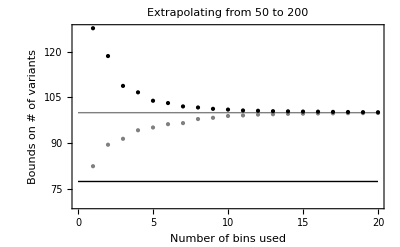

```mathematica
start=output[[1,2,1]]
exact=output[[1,2,2]]
true=exact;

ListPlot[{output[[1;;,2,3]]100 /exact,output[[1;;,2,4]]100/exact},Joined->False,PlotStyle->{Gray,Black},Epilog->{Gray,Line[{{0,100},{maxbins,100}}],Black,Line[{{0,start*100/exact},{maxbins,start*100/exact}}]},Frame->{True,True,False,False},FrameLabel->{"Number of bins used","Bounds on # of variants"},PlotLabel->"Extrapolating from "<>ToString[nstart]<>" to "<>ToString[nend] ,PlotRange->{0.9 start *100/exact,All}]
```

```mathematica
(*Coarsen by keeping the first d bins. then use the following 2,4,8, etc *)
coarsenSFS[sfs_,cut_]:=Module[{temp,max,curr,d},temp=sfs[[1]][[1;;cut+1]];max=cut+1;d=1;curr=max;While[max<Length[sfs[[1]]],max+=2^d;d+=1;AppendTo[temp,Apply[Plus,sfs[[1]][[(curr+1);;Min[max,Length[sfs[[1]]]]]]]];curr=max
];temp]
coarsenMAT[mat_,cut_]:=Module[{max,temp,d,curr},temp=mat[[1;;cut,1;;]];;max=cut;d=1;curr=max;While[max<Length[mat],max+=2^d;d+=1;AppendTo[temp,Apply[Plus,mat[[(curr+1);;Min[max,Length[mat]]]]]];curr=max
];temp]

extrapolateCoarse2[sampsize_,popsize_,max_,cut_]:=Module[{b,tot,bchpcoarse},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
subcoarse=coarsenSFS[sub,cut];


bchpcoarse=coarsenMAT[bchp,cut];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=LinearProgramming[c,bchpcoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,bchpcoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"];

Return[{Length[bchpcoarse],c.sol,c.solmin}]



]
```

```mathematica
(*Now, add some Poisson noise. Returns an error when no solution is found*)

extrapolatePoisson[sampsize_,popsize_,max_,cut_]:=Module[{b,tot,poisson},totsnp=500000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
(*Build maximum likelihood solution with noise*)
poisson=Map[RandomInteger[PoissonDistribution[#]]&,sub[[1]]];

subcoarse=poisson[[1;;cut+1]];
AppendTo[subcoarse,Apply[Plus,poisson[[cut+2;;]]]];

bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];

Return[{sol,Apply[Plus,poploc[[1,2;;]]],solmin}]



]
```

```mathematica
(*Example application*)
output=ParallelTable[N[extrapolatePoisson[50,500,500,i]],{i,1,8}]
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

{{143977.,199511.,397413.},{160291.,199511.,345173.},{163777.,199511.,278584.},{170427.,199511.,262619.},{176757.,199511.,254578.},{177828.,199511.,237909.},{178708.,199511.,222539.},{Err,199511.,Err}}

```mathematica
(*get a confidence interval from the output!*)
confInt[out_]:=Module[{start,exact,max,min},start=out[[1,1]];exact=out[[1,3]]; minmin=Quantile[out[[2,1;;,1]],0.025]; minmax=Quantile[out[[2,1;;,1]],0.975];maxmax=Quantile[out[[2,1;;,2]],.975];maxmin=Quantile[out[[2,1;;,2]],.025];{start,exact,minmin,minmax,maxmin,maxmax}]
```

```mathematica
(*Now test for accuracy as a function of the number of SNPs*)
```

```mathematica
(*A function to downsample using a hypergeometric distribution (not the expectation, but an actual SNP-by-SNP downsampling. pop should be integer-valued!*) 
HGDownsample[pop_,to_]:=Module[{curr,from,ls,i},from=Length[pop]-1;curr=Table[0,{i,1,to+1}];
For [i=1 (*no need to downsample zeros!*),i≤from-1 (*no need to downsample hom-nonref*),i++,ls=Tally[RandomVariate[HypergeometricDistribution[to,i+1,from],pop⟦i+1⟧]]; Map[curr⟦#⟦1⟧+1⟧+=#⟦2⟧&,ls]];curr⟦1⟧+=pop⟦1⟧;curr⟦-1⟧+=pop⟦-1⟧;Return[curr]  ]


(*Simulation for the effect of finite data: Take a smooth SFS; Poisson Random field sample it; for each SNP in the set and each bootstrap iteration; actually perform a Hypergeometric downsampling.*)
```

```mathematica
(*decrease the bin cutoff until a solution can be found*)

(*utility function for extrapolateBootMonoHypergeo
start: the beginning number of conserved bin
values: the observed SFS
monotony: the matrix defining the monotonicity constraint
monoconst: the vector defining the monotnicity constraint
c:the target vector
bchp: the transfer matrix  

*)

optimizecut[start_,values_,monotony_,monoconst_,c_,bchp_]:=Module[{keeptrying,step,trycut,subcoarse,bmono,cmono,sol,solmin,obs,bchpCoarse},
keeptrying=True;
step=1;(*step size by which to change the cutoff initially*)
trycut=start+step;
While[keeptrying,
trycut=trycut-step;

If[ trycut==0,Break[]];
keeptrying=False;
subcoarse=coarsenSFS[{values}, trycut];
obs=Apply[Plus,subcoarse[[2;;]]];
bchpCoarse=coarsenMAT[bchp,trycut];
bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];

sol=Quiet[Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],keeptrying=True],{LinearProgramming::lpsnf}];
solmin=Quiet[Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],keeptrying=True],{LinearProgramming::lpsnf}]];
If[Not[keeptrying],Return[{obs,sol,solmin,trycut}]];


]


(*Simulation for the effect of finite data: Take a smooth SFS; Poisson Random field sample it; for each SNP in the set and each bootstrap iteration; actually perform a Hypergeometric downsampling. Assumes a monotonicity constraint*)

(*sampsize: the sample size we are extrapolating from
popsize: the population size we are extrapolating to
max: The size of the total population--setting this higher may increase accuracy, but also increases compute time.
cut: the number of rare variant bins to keep uncollapsed
nboot: The number of uncollapsed bins at the rare end of the spectrum
totsnp=the total number of nonref SNPs in the population
	propmon: the proportion of bins in the underlying frequency spectrum where we impose a decreasing spectrum with frequency (0 is the "stanard" LP) 

*)

extrapolateBootMonoHypergeo[sampsize_,popsize_,max_,startcut_,nboot_,totsnp_,propmon_]:=Module[{b,tot,pop,poisson,nmono,bloc,poploc,bchp,sub,monotony,monoconst,obs,exact,sol,solmin,trycut,subcoarse,boots,c,bchpCoarse,ret1},

pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;

poisson=pop;(*Remnant of a previous version wherein we implemented the poisson resampling at the max population. Now this is performed below*)
nmono=Round[propmon*popsize];

monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{nmono+1,popsize}]⟦2;;,1;;⟧; (*We do not want to impose a constraint on zerotons, hence the 2;;*)
monoconst=Table[{0,1},{it,1 ,nmono}];
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

(*Now that the pathological cases have ben dealt with, we can focus on the actual extrapolation problem*)

(*Projection matrices*)
b=mat[max,popsize]; 
bloc=mat[popsize,sampsize];
(*projection matrix without zerotons*)
bchp=bloc[[2;;,2;;]];


poploc=Transpose[Dot[b,Transpose[poisson]]];
(*Poisson sample the distribution to simulate the finite genome*)
poploc={Map[RandomInteger[PoissonDistribution[#]]&,poploc[[1]]]};


(*Perform downsampling*)
(*sub=HGDownsample[poploc⟦1⟧,sampsize];*)

(*obs=Apply[Plus,subcoarse[[2;;]]];(*The number of observed nonref variants*) *)
exact=Apply[Plus,poploc[[1,2;;]]]; (*The number of nonref variants in the true population*)

(*Now that we have our simulated sample, we can proceed with the LP solution*)

(*Coarsen the SFS and the projection matrix*)
(*subcoarse=coarsenSFS[{sub}, startcut];
bchpCoarse=coarsenMAT[bchp,startcut];*)

c=Table[1,{i,1,popsize}];(*target vector*)
ret1={exact};
boots=ParallelTable[
RandomSeed[i];
sub=HGDownsample[poploc⟦1⟧,sampsize];
{obs,sol,solmin,trycut}=optimizecut[startcut,sub,monotony,monoconst,c,bchp];

{obs,exact,sol,solmin,trycut}
,{i,1,nboot}];


Return[{ret1,boots}]
]
```

```mathematica
SeedRandom[1]
targetSizes={100,200,400,1000};
smallestlog=3;
largestlog=8;
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}];

runextrap[targetsize_,Ls_,nboot_]:=Module[{},
start=50; (*sample size*)
target=targetsize; (*target size*)
max=target; (*population size*)
 
fmono=0.0; (*frequency range over which the SFS is forced monotonic*)
startcut=16; (*The starting point for the cut.*)
sizes=Ls;
Table[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]
]
```

```mathematica
Timing[out50T100=runextrap[100,sizes,40];]
Timing[out50T200=runextrap[200,sizes,40];]
Timing[out50T400=runextrap[400,sizes,40];]
Timing[out50T1000=runextrap[1000,sizes,40];]
```

{99.072973,Null}

{205.2757,Null}

{152.37657,Null}

{413.47133,Null}

```mathematica
start=50;
target=200;
max=200;
nboot=40;
fmono=0;
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]

out50T200=Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}];
```

```mathematica
start=50
target=1000
max=1000
nboot=40
fmono=0.1
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
out50T1000=ParallelTable[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8},{fmono,{0,0.005,0.01,0.02}}];
```

```mathematica
start=50
target=300
max=target
nboot=40
fmono=0
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
(*Here we just run f=0*)
out50T300={Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]};
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T300",out50T300]
start=50
target=350
max=350
nboot=40
fmono=0
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
(*Here we just run f=0*)
out50T350={Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]};
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T350",out50T350]
```

50

300

300

40

0

3

8

{1000,10000,100000,1000000,10000000,100000000}

3

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

4

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

5

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

6

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

7

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

8

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

50

350

350

40

0

3

8

{1000,10000,100000,1000000,10000000,100000000}

3

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

4

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

5

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

6

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

7

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

8

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

```mathematica
start=50
target=400
max=400
nboot=40
fmono=0.1
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
out50T400=ParallelTable[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8},{fmono,{0,0.005,0.01,0.02}}];
```

```mathematica
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T200",out50T200]
```

```mathematica
(*Save to file.*)
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T100",out50T100]
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T400",out50T400]
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T1000",out50T1000]
```

```mathematica
(*Load from file if exists*)
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T100"];
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T400"];
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T1000"];
```

```mathematica
(*get a confidence interval from the output!*)
confInt2[out_]:=Module[{start,exact,max,min},start=Mean[out[[2,1;;,1]]];exact=out[[1,1]]; minmin=Quantile[out[[2,1;;,3]],0.025]; minmax=Quantile[out[[2,1;;,3]],0.975];maxmax=Quantile[out[[2,1;;,4]],.975];maxmin=Quantile[out[[2,1;;,4]],.025];{start,exact,minmin,minmax,maxmin,maxmax}]

dattoCI[dat_]:=Map[confInt2,dat[[1;;]]]




plot50T100=N[dattoCI[out50T100]];
plot50T200=N[dattoCI[out50T200]];
plot50T400=N[dattoCI[out50T400]];
plot50T1000=N[dattoCI[out50T1000]];
```

```mathematica
offsetscale=0.1;
colors={Red, Purple,Blue, Gray}


h=Graphics[Line[{{0,-.02},{0,.02}}]];
h1=Graphics[Line[.15*{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]];
arrstylelow=Arrowheads[{{.1,0,{h1,.01}},{.1,1,{h,.01}}}];
arrstyleup=Arrowheads[{{-.1,1,{h1,.01}},{.1,0,{h,.01}}}];

plotout[plotDatavec_,sizes_,range_]:=Module[{barsmin2,barsmax2,plotDataS,enum,nExt,offsetnum,means},
nExt=Length[plotDatavec];
allbarsmin={};
allbarsmax={};
means={};
For[enum=1,enum≤nExt,enum++,
plotDataS=plotDatavec⟦enum⟧;
offsetnum=-nExt/2+enum;
AppendTo[allbarsmin,Table[{colors⟦enum⟧,arrstylelow, Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[allbarsmax,Table[{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[means,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧];
];
(*observed values*)

ListPlot[Join[{Table[{x,1},{x,2,8}]},Table[Table[{x,means⟦i⟧},{x,2,8}],{i,1,nExt}]],Joined->True,Epilog->{Join[allbarsmin,allbarsmax],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->range,PlotStyle->Join[{Black},Table[{Dashed,colors⟦i⟧},{i,1,nExt}]],Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"log10(number of SNPs)","Predicted and observed counts (proportion of correct value)" }]]
```

{RGBColor[1,0,0],RGBColor[0.5,0,0.5],RGBColor[0,0,1],GrayLevel[0.5]}

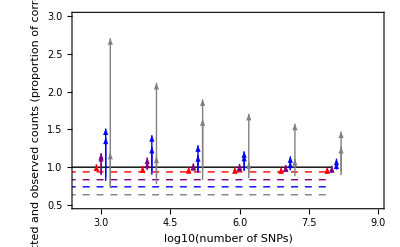

```mathematica
plotout[{plot50T100,plot50T200,plot50T400,plot50T1000},sizes,{{2.5,9},{.5,3}}]
```

```mathematica
(*Add a run with infinite data*)
extrapolateMonoInfinite[sampsize_,popsize_,max_,startcut_,nboot_,totsnp_,propmon_]:=Module[{b,tot,poisson,nmono,bloc,poploc,bchp,sub,monotony,monoconst,obs,exact,sol,solmin,trycut,subcoarse,boots,c,bchpCoarse,ret1,pop},

pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
(*Poisson= pop for infinite data*)
poisson=pop;
nmono=Round[propmon*popsize];

monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{nmono+1,popsize}]⟦2;;,1;;⟧; (*We do not want to impose a constraint on zerotons, hence the 2;;*)
monoconst=Table[{0,1},{it,1 ,nmono}];
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[poisson]]];

exact=Apply[Plus, poploc⟦1,2;;⟧];

sub=Transpose[Dot[bloc,Transpose[poploc]]];

(*Build maximum likelihood solution with noise*)


(*subcoarse=poisson[[1;;cut+1]];*)

subcoarse=coarsenSFS[sub, startcut];


bchpCoarse=coarsenMAT[bchp,startcut];


obs=Apply[Plus,subcoarse[[2;;]]];

c=Table[1,{i,1,popsize}];

bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];

(*This first run is not really useful--we keep it there for compatibility reasons.*)

sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],"Err"];


ret1={obs,exact,sol,solmin};

boots={};
For[i=1,i≤nboot,i++,
sub=HGDownsample[poploc⟦1⟧,sampsize];
{obs,sol,solmin,trycut}=optimizecut[startcut,sub,monotony,monoconst,c,bchp];

(*Print[N[{obs,exact,sol,solmin,trycut,nmono}]];*)
AppendTo[boots,{obs,exact,sol,solmin,trycut}];
];



Return[{ret1,boots}]
]
```

```mathematica
start=50;
target=1000;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T1000=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{61.0951,100.,94.9884,105.117},{}},{{61.0951,100.,95.4084,103.56},{}},{{61.0951,100.,95.4907,102.647},{}},{{61.0951,100.,96.1199,102.483},{}}}

```mathematica
start=50;
target=200;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T200=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{77.4879,100.,99.984,100.013},{}},{{77.4879,100.,99.984,100.011},{}},{{77.4879,100.,99.9928,100.011},{}},{{77.4879,100.,99.9931,100.006},{}}}

```mathematica
start=50;
target=400;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T400=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]

start=50;
target=100;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T100=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{69.5127,100.,99.4772,100.504},{}},{{69.5127,100.,99.4772,100.228},{}},{{69.5127,100.,99.7002,100.226},{}},{{69.5127,100.,99.77,100.181},{}}}

{{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}}}

{{{87.3881,100.,100.,100.},{}},{{77.4879,100.,99.984,100.013},{}},{{69.5127,100.,99.4772,100.504},{}},{{61.0951,100.,94.9884,105.117},{}}}

```mathematica
offsetscale=0.1;
colors={Orange,Red, Purple,Blue}
plotout[plotDatavec_,sizes_,range_,inf_]:=
Module[{barsmin2,barsmax2,plotDataS,enum,nExt,offsetnum,means},
nExt=Length[plotDatavec];
allbarsmin={};
allbarsmax={};
means={};
For[enum=1,enum≤nExt,enum++,
plotDataS=plotDatavec⟦enum⟧;
offsetnum=-nExt/2+enum;
AppendTo[allbarsmin,Table[{colors⟦enum⟧,arrstylelow, Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[allbarsmax,Table[{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[means,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧];
];
(*Put infinite-limit data*)

infOffset=1;
AppendTo[allbarsmin,Table[offsetnum=-nExt/2+enum-0.5;{colors⟦enum⟧,arrstylelow,Arrow[{{Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,3]]/inf[[enum,1,2]]}, {Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,3]]/inf[[enum,1,2]]+10^-9 (*pseudocount to avoid size zero drawing*)}}]},{enum,1,nExt}]];
AppendTo[allbarsmax,Table[offsetnum=-nExt/2+enum-0.5;{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,4]]/inf[[enum,1,2]]}, {Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,4]]/inf[[enum,1,2]]+10^-9}}]},{enum,1,nExt}]];

ListPlot[Join[{Table[{x,1},{x,2,8.2,.1}],Table[{x,1},{x,8.8,9.2,.1}]},Table[Table[{x,means⟦i⟧},{x,2,8.2,.1}],{i,1,nExt}],Table[Table[{x,means⟦i⟧},{x,8.8,9.2,.1}],{i,1,nExt} ]],Joined->True,Epilog->{Join[allbarsmin,allbarsmax],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->range,PlotStyle->Join[{Black,Black},Table[{Dashed,colors⟦i⟧},{i,1,nExt}],Table[{Dashed,colors⟦i⟧},{i,1,nExt}]],Frame->{True,True,False,False},FrameStyle->Directive[13],FrameTicks->{{{3,Superscript[10,3]},{4,Superscript[10,4]},{5,Superscript[10,5]},{6,Superscript[10,6]},{7,Superscript[10,7]},{8,Superscript[10,8]},{9,∞}},Automatic},FrameLabel->{"number of SNPs","Relative confidence interval" },BaseStyle->{Large,FontFamily->"Arial"}]]
```

{RGBColor[1,0.5,0],RGBColor[1,0,0],RGBColor[0.5,0,0.5],RGBColor[0,0,1]}

{{{87.3881,100.,100.,100.},{}},{{77.4879,100.,99.984,100.013},{}},{{69.5127,100.,99.4772,100.504},{}},{{61.0951,100.,94.9884,105.117},{}}}

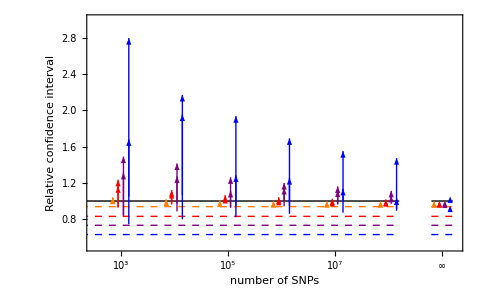

```mathematica
infNoF={inf50T100⟦1⟧,inf50T200⟦1⟧,inf50T400⟦1⟧,inf50T1000⟦1⟧}
Nexpplot=plotout[{plot50T100⟦1⟧,plot50T200⟦1⟧,plot50T400⟦1⟧,plot50T1000⟦1⟧},sizes,{{2.5,9.25},{.5,3}},infNoF]
```

```mathematica
Export["~/Dropbox/capture_recapture/figures/LvsNn.pdf",Nexpplot]
Export["~/Dropbox/capture_recapture/figures/LvsNn.eps",Nexpplot]
```

~/Dropbox/capture_recapture/figures/LvsNn.pdf

~/Dropbox/capture_recapture/figures/LvsNn.eps